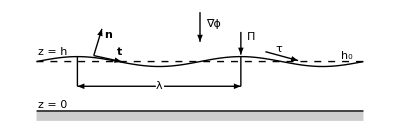

```mathematica
h0=.5;
a=-1;
b=1;
λ=1;
A=0.05;
f[x_]:=A*Sin[(2π/λ) x]+h0
x1=-0.65;
length = 0.17;
Show[Plot[{A*Sin[(2π/λ) x]+h0,0},{x,a,b},PlotRange->{-0.1,1},PlotStyle->{Directive[Black,Thick]},Axes->False,Filling->{2->Bottom}],
Graphics[{Arrowheads[Medium],Arrow[{{0,1},{0,0.7}}],Arrow[{{1/4,.8},{1/4,0.57}}],Arrow[{{.4,.6},{.6,0.51}}],Text[Style["∇ϕ",Medium,Black],{.08,.88}],Text[Style["Π",Medium,Black],{.31,.75}],Text[Style["τ",Medium,Black],{.48,.63}],Text[Style["h_0",Medium,Black],{.9,.56}],Dashed,Line[{{a,h0},{b,h0}}]}],Graphics[{Arrowheads[Medium],Line[{{-3/4,h0+A},{-3/4,h0/2}}],Line[{{1/4,h0+A},{1/4,h0/2}}],Text[Style["λ",Black,Medium],{-1/4,h0/2}],Arrow[{{-.22,h0/2},{1/4,h0/2}}],Arrow[{{-.27,h0/2},{-3/4,h0/2}}],Arrow[{{x1,f[x1]+0.02},{x1+0.05,f[x1]-0.05/f'[x1]+0.02}}],Arrow[{{x1,f[x1]+0.02},{x1+length,f[x1]+length*f'[x1]-0.01}}],Text[Style["n",Black,Bold,Medium],{x1+0.09,f[x1]+0.23}],Text[Style["t",Black,Bold,Medium],{x1+0.16,f[x1]+0.06}],Text[Style["z = 0",Black, Medium],{-.9,0.06}],Text[Style["z = h", Black, Medium],{-.9,h0+.1}]}],AspectRatio->1/3]
```

```mathematica
??Filling
```

Filling is an option for ListPlot, Plot, Plot3D, and related functions that specifies what filling to add under points, curves, and surfaces.

Attributes[Filling]={Protected}